```mathematica
(* Interpolation *)
```

```mathematica
data = Import["E:\\2019spr\\近代物理实验\\MyReport\\0505_curie\\1.txt","Table"];
```

```mathematica
f = Interpolation[data,Method->"Spline",InterpolationOrder->5];
(* Method option:
     Spline - continuous derivative
   Hermite - non-continuous drv.
*)
```

```mathematica
df= D[f[x],x];
```

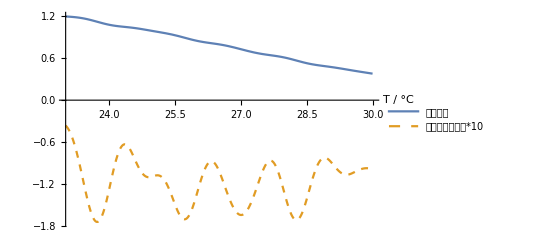

```mathematica
Plot[{f[x],df*10},{x,23,30},PlotStyle->{Automatic,Dashed},PlotLegends->Placed[{"原始数据","插值后数值导数*10"},{0.75,0.9}],AxesLabel->{"T / °C",""}]
```

```mathematica
(* Fitting *)
Clear[a,b,c,d]
func[a_,b_,c_,d_]:=a*E^(-b*(x-c)^2)+d;
```

```mathematica
f2 = FindFit[data,{func[a,b,c,d]},{{a,1.4},{b,0.01},{c,18},{d,0}},{x}];
```

```mathematica
param={a,b,c,d}/.f2
```

{1.37683,0.0112191,19.1515,0.0270794}

```mathematica
ffit=Apply[func,param];
```

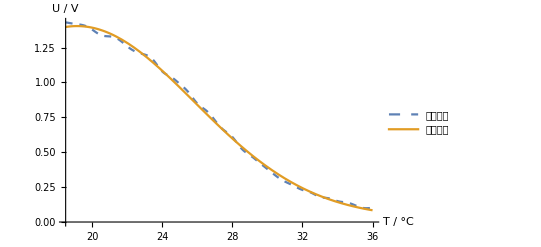

```mathematica
Plot[{f[x],ffit},{x,18.5,36},PlotStyle->{Dashed,Automatic},PlotLegends->Placed[{"原始数据","高斯拟合"},{0.8,0.8}],AxesLabel->{"T / °C","U / V"}]
```